```mathematica
u[t] = (x[t]^{1- η} -1)/(1- η)
```

{(-1+x[t]^(1-η))/(1-η)}

```mathematica
p[t] = u[t]/.x[t]-> B*(δ - r*(1-η))/η*e^{(r(1-η)-δ)t/η}
```

{{(-1+((B e^((t (-δ+r (1-η)))/η) (δ-r (1-η)))/η)^(1-η))/(1-η)}}

```mathematica
(*Takes too long to integrate as such why?*)
Integrate[p[t]*e^{-δ*t}, {t, 0, Infinity }]
```

$Aborted

```mathematica
p[t]
```

{{(-1+((B e^((t (-δ+r (1-η)))/η) (δ-r (1-η)))/η)^(1-η))/(1-η)}}

```mathematica
p[t] * t
```

{{(t (-1+((B e^((t (-δ+r (1-η)))/η) (δ-r (1-η)))/η)^(1-η)))/(1-η)}}

```mathematica
Clear[u[t]]
```

Clear::ssym: u[t] is not a symbol or a string.

```mathematica
u[t]
```

{(-1+x[t]^(1-η))/(1-η)}

```mathematica
p[t] = u[t][[1]]/.x[t]-> B*(δ - r*(1-η))/η*Exp[(r-δ)t/η]
```

(-1+((B ⅇ^((t (r-δ))/η) (δ-r (1-η)))/η)^(1-η))/(1-η)

```mathematica
p[t]
```

(-1+((B ⅇ^((t (r-δ))/η) (δ-r (1-η)))/η)^(1-η))/(1-η)

```mathematica
Integrate[(-1+((B ⅇ^((t (r-δ))/η) (δ-r (1-η)))/η)^(1-η))/(1-η)*Exp[(-δ * t)],  {t, 0 , Infinity}]
```

ConditionalExpression[(1/δ-B ((B (δ+r (-1+η)))/η)^-η)/(-1+η), Re[(r-δ-r η)/η]<0&&Re[δ]>0]

```mathematica
Assumptions = {η>1}
```

Set::wrsym: Symbol Assumptions is Protected.

```mathematica
{η>1}
u[t]=(1/δ-B ((B (δ+r (-1+η)))/η)^-η)/(-1+η)
```

{η>1}

(1/δ-B ((B (δ+r (-1+η)))/η)^-η)/(-1+η)

```mathematica
u[t]
```

(1/δ-B ((B (δ+r (-1+η)))/η)^-η)/(-1+η)

```mathematica
x[t_, B_, δ_, η_,r_]= B*(δ - r*(1-η))/η*Exp[(r-δ)t/η]
```

(B ⅇ^((t (r-δ))/η) (δ-r (1-η)))/η

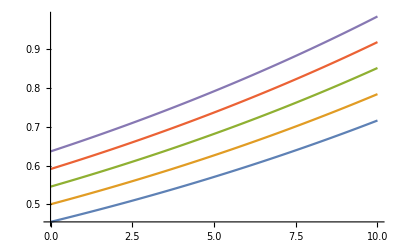

```mathematica
Plot[Evaluate@Table[x[0,100,δ,eta,0.05],{δ, 0,0.0020, 0.0005 }],{t,0,10}]
```

```mathematica
f[a_,b_,c_,d_]=a+Sin[b]*Exp[c]-d^4
```

a-d^4+ⅇ^c Sin[b]

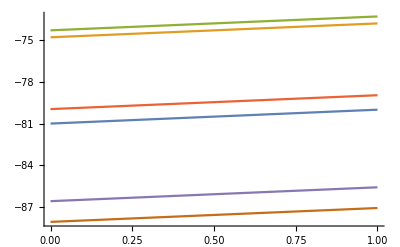

```mathematica
Plot[Evaluate@Table[f[a,b,2,3],{b,0,5,1}],{a,0,1}]
```

```mathematica
x[t, 1,0.1, 2,5]
```

2.55 e^(-2.55 t)

```mathematica
x[t, 1,1, 2,5]
```

3 e^(-3 t)

```mathematica
x[t, 1,0, 2,5]
```

5/2 e^(-5 t/2)

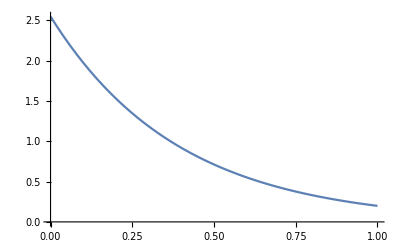

```mathematica
Plot[x[t, 1,0.1, 2,5],{t,0,1}]
```

```mathematica
x[0, 1,0, 2,5]
```

5/2

```mathematica
x[1, 1,0, 2,5]
```

5/(2 e^(5/2))

```mathematica
Plot
```

```mathematica
100/6
```

```mathematica
50/3
N[t0/3]
```

50/3

0.333333 t0

```mathematica
N[50/3]
```

```mathematica
16.666666666666668
N[δ, δ = 1]
```

16.6667

1

```mathematica
x[t_, B_, δ_, η_,r_]= B*(1+r)/r * (δ - r*(1-η))/η*Exp[(r-δ)t/η]
```

(B ⅇ^((t (r-δ))/η) (1+r) (δ-r (1-η)))/(r η)

(B ⅇ^((t (-δ+r (1-η)))/η) (1+r) (δ-r (1-η)))/(r η)

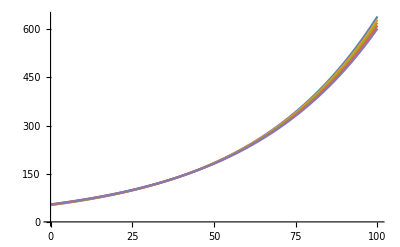

```mathematica
(B ⅇ^((t (-δ+r (1-η)))/η) (1+r) (δ-r (1-η)))/(r η)
Plot[Evaluate@Table[x[t,100,δ,2,0.05],{δ, 0,0.0020, 0.0005 }],{t,0,100}]
```

```mathematica
ySolved = DSolve[y'[t] - r*y[t] == Subscript[p, 0]^(-1/η)*Exp[(r-δ)/η*t] && y[0] == B, y[t],t]// FullSimplify
```

{{y[t]→(ⅇ^(r t) p_0^(-1/η) (η-ⅇ^(-(t (δ+r (-1+η)))/η) η+B (δ+r (-1+η)) p_0^(1/η)))/(δ+r (-1+η))}}

```mathematica
ySolved
```

{{y[t]→(ⅇ^(r t) p_0^(-1/η) (η-ⅇ^(-(t (δ+r (-1+η)))/η) η+B (δ+r (-1+η)) p_0^(1/η)))/(δ+r (-1+η))}}

```mathematica
y [t] /. ySolved
```

{(ⅇ^(r t) p_0^(-1/η) (η-ⅇ^(-(t (δ+r (-1+η)))/η) η+B (δ+r (-1+η)) p_0^(1/η)))/(δ+r (-1+η))}

```mathematica
y[t]
```

y[t]

```mathematica
$Assumptions = B>=0 && η>=0 && δ>=0 && r>=0&& Subscript[p, o]>=0
```

B≥0&&η≥0&&δ≥0&&r≥0&&p_o≥0

```mathematica
Limit[(y [t] /. ySolved )* Exp[-r*t], t -> Infinity]
```

{ConditionalExpression[B+(η p_0^(-1/η))/(δ+r (-1+η)), (p_0^(-1/η)|B p_0^(1/η))∈ℝ&&δ+r η>r]}

```mathematica
y[t]
```

```mathematica
m[t] = ⅇ^(r t) C[1]-(ⅇ^(r t-(t (δ+r (-1+η)))/η) η Subscript[p, 0]^(-1/η))/(δ+r (-1+η))
```

ⅇ^(r t) C[1]-(ⅇ^(r t-(t (δ+r (-1+η)))/η) η p_0^(-1/η))/(δ+r (-1+η))

```mathematica
Limit[m[t],t -> Infinity]
```

ConditionalExpression[∞, p_0^(-1/η)∈ℝ&&r>0&&η≠0&&r η<δ η&&C[1]>0]

```mathematica
m[t_,a_,b_,δ_,r_, η_] = ⅇ^(r t) * a-(ⅇ^(r t-(t (δ+r (-1+η)))/η) η b^(-1/η))/(δ+r (-1+η))
```

a ⅇ^(r t)-(b^(-1/η) ⅇ^(r t-(t (δ+r (-1+η)))/η) η)/(δ+r (-1+η))

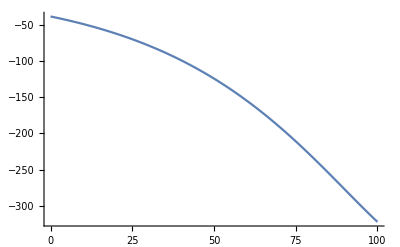

```mathematica
Plot[m[t,1,1, 0.0005,0.05, 2],{t,0,100}]
```

```mathematica
m[t,a,b,δ,r, η]
```

a ⅇ^(r t)-(b^(-1/η) ⅇ^(r t-(t (δ+r (-1+η)))/η) η)/(δ+r (-1+η))

```mathematica
m[t,1,1, 0.0005,0.05, 2]
```

m[t,1,1,0.0005,0.05,2]

```mathematica
N[m[0,1,1, 0.0005,0.05, 2]]
```

m[0.,1.,1.,0.0005,0.05,2.]

```mathematica
m[t,1,1, 0.0005,0.05, 2]
```

```mathematica
m[t,a,b,δ,r, η]
```

```mathematica
a ⅇ^(r t)-(b^(-1/η) ⅇ^(r t-(t (δ+r (-1+η)))/η) η)/(δ+r (-1+η))
```

```mathematica
m[t] = ⅇ^(r t) C[1]-(ⅇ^(r t-(t (δ+r (-1+η)))/η) η Subscript[p, 0]^(-1/η))/(δ+r (-1+η))
```

ⅇ^(r t) C[1]-(ⅇ^(r t-(t (δ+r (-1+η)))/η) η p_0^(-1/η))/(δ+r (-1+η))

```mathematica
f[t] = m[t]* Exp[-r*t]
```

ⅇ^(-r t) (ⅇ^(r t) C[1]-(ⅇ^(r t-(t (δ+r (-1+η)))/η) η p_0^(-1/η))/(δ+r (-1+η)))

```mathematica
Limit[f[t],t -> Infinity]
```

```mathematica
ySolved = DSolve[y'[t] - r*y[t] == Subscript[p, 0]^(-1/η)*Exp[(r-δ)/η*t] + ϕ && y[0] == B, y[t],t]// FullSimplify
```

{{y[t]→(-ϕ+ⅇ^(r t) (B r+ϕ))/r+(ⅇ^(-(t δ)/η) (ⅇ^(t (r+δ/η))-ⅇ^((r t)/η)) η p_0^(-1/η))/(δ+r (-1+η))}}

```mathematica
$Assumptions = B>=0 && η>=0 && δ>=0 && r>=0&& Subscript[p, o]>=0 && ϕ>=0
```

```mathematica
B≥0&&η≥0&&δ≥0&&r≥0&&Subscript[p, o]≥0&&ϕ≥0
Limit[(y [t] /. ySolved )* Exp[-r*t], t -> Infinity]
```

B≥0&&η≥0&&δ≥0&&r≥0&&p_o≥0&&ϕ≥0

{ConditionalExpression[B+ϕ/r+(η p_0^(-1/η))/(δ+r (-1+η)), ]}

```mathematica
pSolve = Solve[B+ϕ/r+(η Subscript[p, 0]^(-1/η))/(δ+r (-1+η))== 0 ,Subscript[p, 0]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p_0→(r-δ-r η)^-η ((B+ϕ/r)/η)^-η}}

```mathematica
x[t] = Subscript[p, 0]^(-1/η)Exp[(r - δ)/η*t]
```

ⅇ^((t (r-δ))/η) p_0^(-1/η)

```mathematica
xSchedule[t_, B_, δ_, r_, ϕ_] = x[t]/.pSolve// FullSimplify
```

Set::write: Tag List in {ⅇ^((t (r-δ))/η) (η^η ((r+Times[«2»]+Times[«3»]) (B+Times[«2»]))^-η)^(-1/η)}[t_,B_,δ_,r_,ϕ_] is Protected.

{ⅇ^((t (r-δ))/η) (η^η ((r-δ-r η) (B+ϕ/r))^-η)^(-1/η)}

```mathematica
xSchedule[t_, B_, δ_, r_, ϕ_]
```

{ⅇ^((t (r-δ))/η) (η^η ((r-δ-r η) (B+ϕ/r))^-η)^(-1/η)}[t_,B_,δ_,r_,ϕ_]

```mathematica
xOptim[t_, B_, δ_, η_, r_, ϕ_]  = (B + ϕ/r)(δ +r(1-η))/η*Exp[(r - δ)/η*t]
```

(ⅇ^((t (r-δ))/η) (δ+r (1-η)) (B+ϕ/r))/η

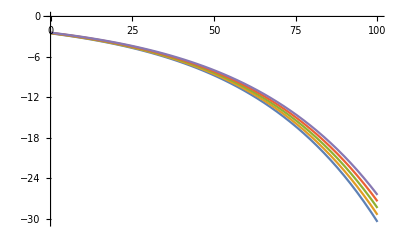

```mathematica
Plot[Evaluate@Table[xOptim[t,100,δ,2,0.05, 0],{δ, 0,0.0020, 0.0005 }],{t,0,100}]
```

```mathematica
x[t_]:= B(1+ 1/(1-1/(1+r)^10))(δ + η*r -r)/η* Exp[(r - δ)/η*t]
```

```mathematica
mSolve10 =DSolve[{m'[t]== r*m[t] - x[t],m[0]==B},m[t], t]//FullSimplify
```

{{m[t]→-((B ⅇ^((t (r-δ))/η) (-1+ⅇ^((t (δ+r (-1+η)))/η) (1+r)^10-2 r (2+r) (1+r (1+r) (2+r (2+r))) (5+r (10+r (10+r (5+r))))))/(r (2+r) (1+r (1+r) (2+r (2+r))) (5+r (10+r (10+r (5+r))))))}}

```mathematica
Plot[Piecewise[{{mSolve10[t],0<=t<10},{mSolve20[t],10<=t<20}}{t,0,20}]
```

```mathematica
f[t]=100*ⅇ^(r t-(t (δ+r (-1+η)))/η)
```

100 ⅇ^(r t-(t (δ+r (-1+η)))/η)

```mathematica
B = 100
```

100

```mathematica
Clear[r]
g[t_] = Piecewise[{{100*ⅇ^(r t-(t (δ+r (-1+η)))/η),0<=t<10},{100*ⅇ^(r t-(t (δ+r (-1+η)))/η)+ 100,t=10}, {100*ⅇ^(r t-(t (δ+r (-1+η)))/η),10<t<=20}}]
```

Piecewise[{{100 ⅇ^(10 r-(10 (δ+r (-1+η)))/η) (1+1/r), 10}, {0, True}}]

```mathematica
Manipulate[Plot[100*ⅇ^(r t-(t (δ+r (-1+η)))/η),{t,0,10}],{η,1.1,2},{r,0.005,0.05},{δ,0,0.0090}]
```

```mathematica
g[t]
```

g[t]

```mathematica
SubStar[m][10]
```

100 ⅇ^(10 r-(10 (δ+r (-1+η)))/η)

```mathematica
Manipulate[Plot[Exp[-r*t],{t,0,1000}], {r, 0.005, 0.05}]
```

```mathematica
SubStar[n][t_]:=100*ⅇ^(0.05* t-(t (0.0020+0.05 (-1+2))/2)
```

```mathematica
Plot[SubStar[n][t],{t,0,10}]
```

-Graphics-

```mathematica
N[SubStar[n][0]]
```

```mathematica
SubStar[n][0.]
SubStar[n]
```

n_*[0.]

```mathematica
SubStar[n][t_]
```

n_*[t_]